```mathematica
PlotSurf[surffname_]:=Module[{surfs,surfshapes},
surfs=Import[surffname, "Table",HeaderLines->9, "FieldSeperators"->" ", "LineSeperators"->"\n"];
surfshapes=Flatten@Table[Line[{{s[[2]],s[[3]]},{s[[4]],s[[5]]}}],{s,surfs}];
Graphics[Join[{Directive[{Thin,Red}]},surfshapes],ImageSize->Large]
]
```

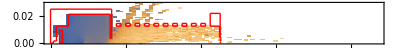

```mathematica
data=Import["/home/cal/Documents/DSMC_Simulations/5_13_20_density_control/flow_2.000_gap_0.005_len_0.000/data/stats_omega_0.csv","Table",HeaderLines->1,"FieldSeparators"->","];
surfs=PlotSurf["/home/cal/Documents/DSMC_Simulations/5_13_20_density_control/flow_2.000_gap_0.005_len_0.000/data/cell.510001.surfs"];
(*data=Select[data,#[[3]]>0.00001&];*)
data=data/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_}/;c<0.0001->{a,b,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000};
z=data[[;;,1]];
r=data[[;;,2]];
n=data[[;;,3]];
t=data[[;;,4]];
tσ=√data[[;;,5]];
vr=data[[;;,6]];
vz=data[[;;,7]];
vrσ=√data[[;;,8]];
vzσ=data[[;;,9]];
cov=data[[;;,10]];
d=vz;
Show[ListDensityPlot[Transpose@{r,z,d},PlotRange->{(Sort@DeleteDuplicates[d])[[2]],Max@d},InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->(Max@z)/(Max@r),ImageSize->Full],surfs]
```

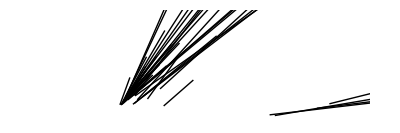

```mathematica
particles=Import["/home/cal/Documents/DSMC_Simulations/5_13_20_density_control/flow_2.000_gap_0.003_len_0.000/particles_omega_0_job_56626765.out","Table",HeaderLines->3,"FieldSeparators"->" "];
r=√(particles[[;;,2]]^2+particles[[;;,3]]^2);
z=particles[[;;,4]];
r2=√(particles[[;;,5]]^2+particles[[;;,6]]^2);
z2=particles[[;;,7]];
lines = Table[Line[{{z[[i]],r[[i]]},{z2[[i]],r2[[i]]}}],{i,Length@z}];
Graphics[{Thin,lines},PlotRange->{{0,0.3},{0,0.1}},ImageSize->Full]
```

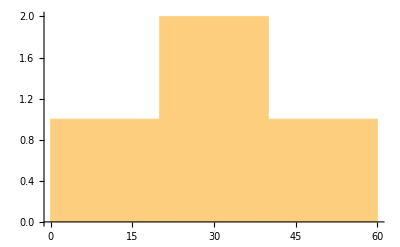

```mathematica
exited=Select[particles,#[[4]]>0.18&];
Histogram[exited[[;;,10]]]
```